# Two-state ET

## Constants

### Unit conversions

```mathematica
au2kcal=627.5095;
kcal2au=1/au2kcal;
ev2cm=8065.54477;
cm2ev = 1/ev2cm ;
au2ev=27.2113 ;
ev2au = 1/au2ev;
cm2au=cm2ev*ev2au;     
au2cm=1/cm2au;
au2ps=2.4189 10^-5;
fs2ps=10^-3;
```

### Universal constants

```mathematica
kb=3.16683 10^-6;
```

```mathematica
β[T_]:=1/(kb T au2kcal);
```

## Reactant and product PMFs (in scaled frame)

We’ll use two parabolas for diabatic potentials as functions of the energy gap coordinate.
Below λ is the reorganization energy, ΔG is the reaction free energy (energy bias), and x is the energy gap coordinate.

```mathematica
Clear[λ,ΔG,f0,ϵ0,ϵi,V]
```

Set the parameters (kcal/mol):

```mathematica
ϵ0=78;
ϵi=1.78;
f0=(4π ϵ0 ϵi)/(ϵ0-ϵi);
λ=23.5;
ΔG=0;
V=0.1;
```

Conversions between scaled coordinate and energy gap coordinate:

```mathematica
x[X_]:=(X-λ-ΔG)/(√(2f0 λ));
X[x_]:=x √(2f0 λ)+λ+ΔG;
```

Minima and crossing point:

```mathematica
XR=λ+ΔG;
XC=0;
XP=-λ+ΔG;
xR=0;
xC=-(ΔG+λ)/(√(2f0 λ));
xP=-√((2λ)/f0);
```

```mathematica
URx[x_]:=1/2 f0 x^2;
UPx[x_]:=1/2 f0(x+√((2λ)/f0))^2+ΔG;
URX[X_]:=1/(4λ)(X-λ-ΔG)^2;
UPX[X_]:=1/(4λ)(X+λ-ΔG)^2+ΔG;
```

Now, the adiabatic states are obtained by diagonalization of the following surrogate Hamiltonian (with V being the electronic coupling):

```mathematica
Hx[x_]:=({{URx[x], V}, {V, UPx[x]}});
HX[X_]:=({{URX[X], V}, {V, UPX[X]}});
```

Adiabatic potentials:

```mathematica
U1x[x_]:=1/2(URx[x]+UPx[x])-1/2 √((URx[x]-UPx[x])^2+4 V^2);
U2x[x_]:=1/2(URx[x]+UPx[x])+1/2 √((URx[x]-UPx[x])^2+4 V^2);
U1X[X_]:=1/2(URX[X]+UPX[X])-1/2 √((URX[X]-UPX[X])^2+4 V^2);
U2X[X_]:=1/2(URX[X]+UPX[X])+1/2 √((URX[X]-UPX[X])^2+4 V^2);
```

Now, plots

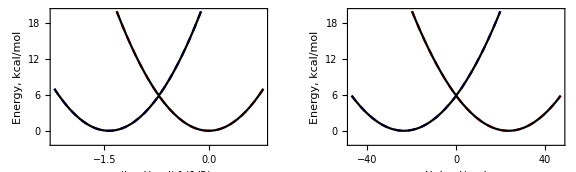

```mathematica
V=0.1;
GraphicsRow[{
Plot[{URx[s],UPx[s],U1x[s],U2x[s]},{s,x[0]-1.5,x[0]+1.5},PlotStyle->{{Red,Dashed},{Blue,Dashed},Black,Black},Axes->{True,False},Frame->True,PlotRange->{-2,20},FrameLabel->{"x, (kcal/mol)^(1/2)","Energy, kcal/mol"}],
Plot[{URX[s],UPX[s],U1X[s],U2X[s]},{s,-2λ,2λ},PlotStyle->{{Red,Dashed},{Blue,Dashed},Black,Black},Axes->{True,False},Frame->True,PlotRange->{-2,20},FrameLabel->{"X, kcal/mol","Energy, kcal/mol"}]
},ImageSize->Large]
```

## Integral TST prefactor

```mathematica
T=300;
```

```mathematica
f1[x_]:=Exp[-β[T]U1x[x]];
f2[x_]:=Exp[-β[T]U1x[x]]+Exp[-β[T]U2x[x]];
```

```mathematica
integ1[x_]:=NIntegrate[f1[y],{y,x,∞}];
integ2[x_]:=NIntegrate[f2[y],{y,x,∞}];
```

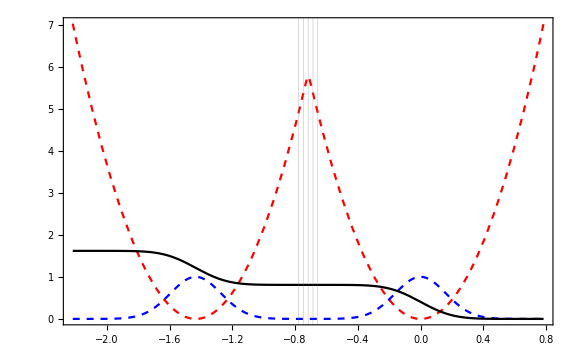

```mathematica
xcminus1=x[XC-1.0];
xcminus2=x[XC-2.0];
xcplus1=x[XC+1.0];
xcplus2=x[XC+2.0];
Plot[{U1x[x],f1[x],2integ1[x]},{x,xC-1.5,xC+1.5},PlotStyle->{{Red,Dashed},{Blue,Dashed},Black,Black},Axes->{True,False},Frame->True,PlotRange->All,GridLines->{{xcminus2,xcminus1,xC,xcplus1,xcplus2},None},ImageSize->Large]
```

```mathematica
integ1/@{xcminus2,xcminus1,xC,xcplus1,xcplus2}
```

{0.404838,0.404832,0.40483,0.404827,0.404822}

```mathematica
integ2/@{xcminus2,xcminus1,xC,xcplus1,xcplus2}
```

{0.404841,0.404835,0.404832,0.404828,0.404822}

## TST rate constant

```mathematica
kTSTapprox1[T_,τO_,τD_,xs_]:=Module[{τL,μ,Ω},
τL=ϵi/ϵ0 τD;
μ=f0 τO τL;
Ω=√(1/(τO τL));
Ω/(2π)Exp[-β[T](U1x[xs]-U1x[xR])]
];
kTSTapprox2[T_,τO_,τD_,xs_]:=Module[{τL,μ,Ω},
τL=ϵi/ϵ0 τD;
μ=f0 τO τL;
Ω=√(1/(τO τL));
Ω/(2π)(Exp[-β[T](U1x[xs]-U1x[xR])]+Exp[-β[T](U1x[xs]-U1x[xR])])
];
```

```mathematica
kTSTexact1[T_,τO_,τD_,xs_]:=Module[{τL,μ,Ω,pref1,pref2},
τL=ϵi/ϵ0 τD;
μ=f0 τO τL;
Ω=√(1/(τO τL));
pref1=1/(√(2π β[T]μ));
pref2=NIntegrate[Exp[-β[T]U1x[x]],{x,xs,∞}];
pref1/pref2 Exp[-β[T]U1x[xs]]
];
kTSTexact2[T_,τO_,τD_,xs_]:=Module[{τL,μ,Ω,pref1,pref2},
τL=ϵi/ϵ0 τD;
μ=f0 τO τL;
Ω=√(1/(τO τL));
pref1=1/(√(2π β[T]μ));
pref2=NIntegrate[Exp[-β[T]U1x[x]]+Exp[-β[T]U2x[x]],{x,xs,∞}];
pref1/pref2(Exp[-β[T]U1x[xs]]+Exp[-β[T]U2x[xs]])
];
```

### How TST rate constants depend on the position of the dividing surface:

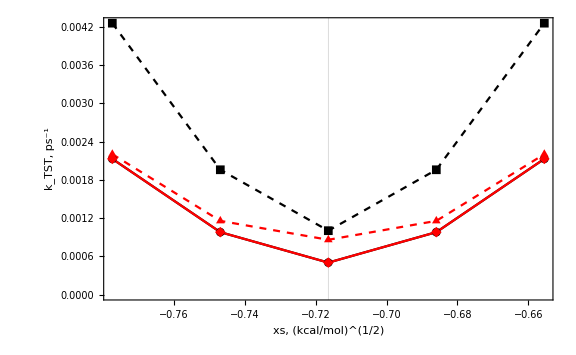

```mathematica
T=300;
τD=8.5;
τO=0.002;
tableApprox1=Table[{xs,kTSTapprox1[T,τO,τD,xs]},{xs,{xcminus2,xcminus1,xC,xcplus1,xcplus2}}];
tableApprox2=Table[{xs,kTSTapprox2[T,τO,τD,xs]},{xs,{xcminus2,xcminus1,xC,xcplus1,xcplus2}}];
tableExact1=Table[{xs,kTSTexact1[T,τO,τD,xs]},{xs,{xcminus2,xcminus1,xC,xcplus1,xcplus2}}];
tableExact2=Table[{xs,kTSTexact2[T,τO,τD,xs]},{xs,{xcminus2,xcminus1,xC,xcplus1,xcplus2}}];
ListLinePlot[{tableApprox1,tableApprox2,tableExact1,tableExact2},PlotStyle->{Black,{Black,Dashed},Red,{Red,Dashed}},ImageSize->Large,PlotRange->All,PlotMarkers->Automatic,Axes->False,Frame->True,FrameLabel->{"xs, (kcal/mol)^(1/2)","k_TST, ps^-1"},GridLines->{{xP,xC,xR},None}]
```